# RD model

```mathematica
Quit[]
```

## Setup

### Set paths

```mathematica
l2mnfile="/Users/xisco/git/TD-PhenHM/chirpy-mk1/RDdata/";
```

## Functions

```mathematica
Amp220n[η_,χ1_,χ2_]:=Module[{},
0.013119832720599923+1.4424686607035737 (1+0.47978032980881324 η) η]
```

```mathematica
Amp221n[η_,χ1_,χ2_]:=Module[{},
0.06151813076119033-0.37822255235046415(1-10.752328588816635η) η]
```

```mathematica
Amp320mn[η_,χ1_,χ2_]:=Module[{},
0.0024090202040443678-0.031253777771474(1-17.10411306587251 η) η]
```

```mathematica
Amp321mn[η_,χ1_,χ2_]:=Module[{},
-0.009314914311472848+0.3291680350575534(1-8.412698657305194η) η+7.75712170204245 η^3]
```

```mathematica
Amp320n[η_,χ1_,χ2_]:=Module[{},
√(5.820540244371564*^-6+(0.015505921290351278-0.9131465613017673 ⅇ^(-0.8705043218490781/η))^2)]
```

```mathematica
Amp321n[η_,χ1_,χ2_]:=Module[{},
√(2.7687486912174918*^-6+(0.010219676743606701-0.7700305247782616 ⅇ^(-0.875497771720061/η))^2)]
```

```mathematica
Phase220n[η_,χ1_,χ2_]:=Module[{},
2.0365412544834065+3.1751175828243294 (-0.18493780685133684-8.34996555486836 η) η]
```

```mathematica
Phase221n[η_,χ1_,χ2_]:=Module[{},
4.910237855711638+1.7022135530428695 (-1.4029268919829936-16.09134030350048 η) η]
```

```mathematica
Phase320mn[η_,χ1_,χ2_]:=Module[{},
0.8136312798427656-0.48457320940397525 ArcTan[700.301840844977 (-0.21895634805616518+η)^2]]
```

```mathematica
Phase321mn[η_,χ1_,χ2_]:=Module[{},
4.610180038601044-1.1630883043998193 ArcTan[15.429146515558246 (-0.10461151062591592+η)]]
```

```mathematica
Phase320n[η_,χ1_,χ2_]:=Module[{},
π+5.9438532099018+2.3636571844421366 ArcTan[10832.16423233716(-0.2514609374102461+η)^3]]
```

```mathematica
Phase321n[η_,χ1_,χ2_]:=Module[{},
4.809964946978988+2.251080063354174 ArcTan[15121.310106029618(-0.23845601138025804+η)^3]]
```

```mathematica
Options[RingDownModel]=Join[Options[OvertoneModelV2],{"t0"->10}];
RingDownModel[η_,χ1_,χ2_,mode_,OptionsPattern[]]:=Module[{amp320n,amp321n,amp220n,x0val,x0mval,x1val,x1mval,res,t0},
t0=OptionValue["t0"];

Which[mode=={2,2},
      x0val=Amp220n[η,χ1,χ2] Exp[(Phase220n[η,χ1,χ2])I];
      x1val=Amp221n[η,χ1,χ2] Exp[(Phase221n[η,χ1,χ2])I];
      res=(OvertoneModelV2[1,{η,χ1,χ2},t0,"Fitα"->{},"Mode"->mode,"Mixing"->{False,{2,2}}])/.x0->x0val/.x1->x1val;,
      
      mode=={3,2},
      x0val=Amp320n[η,χ1,χ2] Exp[(Phase320n[η,χ1,χ2])I];
      x1val=Amp321n[η,χ1,χ2] Exp[(Phase321n[η,χ1,χ2])I];
      x0mval=Amp320mn[η,χ1,χ2] Exp[(Phase320mn[η,χ1,χ2])I];
      x1mval=Amp321mn[η,χ1,χ2] Exp[(Phase321mn[η,χ1,χ2])I];
      res=(OvertoneModelV2[1,{η,χ1,χ2},t0,"Fitα"->{},"Mode"->mode,"Mixing"->{True,{2,2}}])/.x0->x0val/.x1->x1val/.(xm0->x0mval)/.xm1->(x1mval);
];

res
]
```

```mathematica
Options[OvertoneModelV2]={"FixExtra"->True,"Fitα"->{},"Fitτ"->{},"Mode"->{2,2},"Varyω"->False,"Mixing"->{False,{2,2}},"ReIm"->False,"AmpPhase"->False};
OvertoneModelV2[overtones_,pars_,ti_,OptionsPattern[]]:=Block[{ansatz,ampansatz,amphase,fixetra,fitα,fitτ,im,imm,l,m,lm,mm,mixing,mode,modto0,phaseansatz,re,reim,rem,var,varyω,x,y,τs,τsm,α,β,ωm,ωs,ωmτsm,η,χ1,χ2,mixmode},
fixetra=OptionValue["FixExtra"];
fitα=OptionValue["Fitα"];
fitτ=OptionValue["Fitτ"];
mode=OptionValue["Mode"];
varyω=OptionValue["Varyω"];
mixing=OptionValue["Mixing"];
reim=OptionValue["ReIm"];
amphase=OptionValue["AmpPhase"];
{lm,mm}=mixing[[2]];

l=mode[[1]];
m=mode[[2]];
{η,χ1,χ2}=pars[[1;;3]];

(* Freqs. & damping times from Vitor *)
ωs=Table[ωlmn[l,m,n,η,χ1,χ2][[1]],{n,0,overtones}];
If[varyω,ωs=Table[If[n>0,var=RandomReal[{0.98,1.02}],var=1];var*ωlmn[l,m,n,η,χ1,χ2][[1]],{n,0,overtones}]];
τs=Table[ωlmn[l,m,n,η,χ1,χ2][[2]],{n,0,overtones}];

If[Not@amphase,
ansatz=Sum[If[Not@reim,x=ToExpression["x"<>ToString[n]],x=ToExpression[("x"<>ToString[n]+I "y"<>ToString[n])]]; x Exp[-(t-ti)/(τs[[n+1]](1+ToExpression["β"<>ToString[n]]))] (Cos[ωs[[n+1]](1+ToExpression["α"<>ToString[n]]) (t)]+I Sin[ ωs[[n+1]](1+ToExpression["α"<>ToString[n]]) (t)] ),{n,0,overtones}];
If[mixing[[1]],
ωmτsm=Table[ωlmn[lm,mm,n,η,χ1,χ2],{n,0,overtones}];
ωm=ωmτsm[[All,1]];
τsm=ωmτsm[[All,2]];
ansatz=ansatz+Sum[If[Not@reim,x=ToExpression["xm"<>ToString[n]],x=ToExpression["xm"<>ToString[n]]+I ToExpression["ym"<>ToString[n]]];x Exp[-(t-ti)/(τsm[[n+1]])] (Cos[ωm[[n+1]] (t)]+I Sin[ ωm[[n+1]] (t)] ),{n,0,overtones}]];,

re=Sum[ToExpression["x"<>ToString[n]] Exp[-(t-ti)/(τs[[n+1]](1+ToExpression["β"<>ToString[n]]))]Cos[ωs[[n+1]](1+ToExpression["α"<>ToString[n]]) (t)+ToExpression["ϕ"<>ToString[n]]],{n,0,overtones}];
im=Sum[ToExpression["x"<>ToString[n]] Exp[-(t-ti)/(τs[[n+1]](1+ToExpression["β"<>ToString[n]]))]Sin[ωs[[n+1]](1+ToExpression["α"<>ToString[n]]) (t)+ToExpression["ϕ"<>ToString[n]]],{n,0,overtones}];

If[mixing[[1]],
ωmτsm=Table[ωlmn[lm,mm,n,η,χ1,χ2],{n,0,overtones}];
ωm=ωmτsm[[All,1]];
τsm=ωmτsm[[All,2]];
rem=Sum[ToExpression["x"<>ToString[n]] Exp[-(t-ti)/(τsm[[n+1]])] (Cos[ωm[[n+1]] (t)]+I Sin[ ωm[[n+1]] (t)] ),{n,0,overtones}];
imm=Sum[ToExpression["x"<>ToString[n]] Exp[-(t-ti)/(τsm[[n+1]])] (Sin[ωm[[n+1]] (t)]+I Sin[ ωm[[n+1]] (t)] ),{n,0,overtones}];,

rem=0;
imm=0;
];

ampansatz=Sqrt[(re+rem)^2+(im+imm)^2];
phaseansatz=ArcTan[im/re];
ansatz={ampansatz,phaseansatz};
];

modto0=Complement[Table[i,{i,0,overtones}],fitα];
modto0=Table[ToExpression["α"<>ToString[modto0[[i]]]],{i,Length@modto0}];
ansatz=ansatz/.(Table[modto0[[i]]->0,{i,Length@modto0}]);

modto0=Complement[Table[i,{i,0,overtones}],fitτ];
modto0=Table[ToExpression["β"<>ToString[modto0[[i]]]],{i,Length@modto0}];
ansatz=ansatz/.(Table[modto0[[i]]->0,{i,Length@modto0}])
]
```

```mathematica
FinalSpinUIB2017[η_,χ1_,χ2_]:=Module[{m1,m2,S},
m1=1/2 (1+Sqrt[1-4 η]);
m2=1/2 (1-Sqrt[1-4 η]);

S= (m1^2 χ1 + m2^2 χ2)/(m1^2 + m2^2);

(m1^2 χ1 + m2^2 χ2) +(2 Sqrt[3] η+20.0830030082033 η^2-12.333573402277912 η^3)/(1+7.2388440419467335 η)+
 0.3223660562764661 (1-4 η)^0.5 η^2 (1+9.332575956437443 η) (χ1-χ2)-0.059808322561702126 η^3 (χ1-χ2)^2+
(2.3170397514509933 (1-4 η)^0.5 (1-3.2624649875884852 η) η^3 (χ1-χ2) (1/4 (1+Sqrt[1-4 η])^2 χ1+1/4 (1-Sqrt[1-4 η])^2 χ2))/(1/4 (1-Sqrt[1-4 η])^2+1/4 (1+Sqrt[1-4 η])^2)+
(((0. -0.8561951310209386 η-0.09939065676370885 η^2+1.668810429851045 η^3) (1/4 (1+Sqrt[1-4 η])^2 χ1+1/4 (1-Sqrt[1-4 η])^2 χ2))/(1/4 (1-Sqrt[1-4 η])^2+1/4 (1+Sqrt[1-4 η])^2)+((0. +0.5881660363307388 η-2.149269067519131 η^2+3.4768263932898678 η^3) (1/4 (1+Sqrt[1-4 η])^2 χ1+1/4 (1-Sqrt[1-4 η])^2 χ2)^2)/(1/4 (1-Sqrt[1-4 η])^2+1/4 (1+Sqrt[1-4 η])^2)^2+((0. +0.142443244743048 η-0.9598353840147513 η^2+1.9595643107593743 η^3) (1/4 (1+Sqrt[1-4 η])^2 χ1+1/4 (1-Sqrt[1-4 η])^2 χ2)^3)/(1/4 (1-Sqrt[1-4 η])^2+1/4 (1+Sqrt[1-4 η])^2)^3)/(1+((-0.9142232693081653+ 2.3191363426522633 η-9.710576749140989 η^3) (1/4 (1+Sqrt[1-4 η])^2 χ1+1/4 (1-Sqrt[1-4 η])^2 χ2))/(1/4 (1-Sqrt[1-4 η])^2+1/4 (1+Sqrt[1-4 η])^2))]
```

```mathematica
EradUIB2017[η_,χ1_,χ2_]:=Module[{m1,m2,S},
m1=1/2 (1+Sqrt[1-4 η]);
m2=1/2 (1-Sqrt[1-4 η]);

S= (m1^2 χ1 + m2^2 χ2)/(m1^2 + m2^2);

(((1-(2 Sqrt[2])/3) η+0.5609904135313374 η^2-0.84667563764404 η^3+3.145145224278187 η^4) (1+S^3 (-0.6320191645391563+ 4.952698546796005 η-10.023747993978121 η^2)+S^2 (-0.17762802148331427+ 2.176667900182948 η^2)+S (-0.13084389181783257- 1.1387311580238488 η+5.49074464410971 η^2)))/(1+S (-0.9919475346968611+ 0.367620218664352 η+4.274567337924067 η^2))
-0.01978238971523653 S (1-4.91667749015812 η) (1-4 η)^0.5 η (χ1-χ2)-0.09803730445895877 (1-4 η)^0.5 (1-3.2283713377939134 η) η^2 (χ1-χ2)+0.01118530335431078 η^3 (χ1-χ2)^2]
```

```mathematica
ωlmn[l_,m_,n_,η_,χ1_,χ2_]:=Module[{file,data,sp,fmass,fχ,χωτ,ω,τ,llim,ulim},

If[n≤7,
file=l2mnfile<>"l"<>ToString[l]<>"/n"<>ToString[n+1]<>"l"<>ToString[l]<>"m"<>ToString[m]<>".dat";,
file=l2mnfile<>"l"<>ToString[l]<>"/n7l"<>ToString[l]<>"m"<>ToString[m]<>".dat"];
data=Import[file];
χωτ=TakeColumn[data,{1,2,3}];

fmass=1-EradUIB2017[η,χ1,χ2];
fχ=Abs@FinalSpinUIB2017[η,χ1,χ2];

ulim=Flatten[Select[χωτ,#[[1]]≥fχ&,1]];
llim=Flatten[Select[χωτ,#[[1]]-ulim[[1]]<0&][[-1]]];
ω=Mean[Join[{ulim},{llim}]][[2]]/fmass;
τ=Mean[(Abs[1/Join[{ulim},{llim}]]*fmass)][[-1]];
{ω,τ}
]
```

```mathematica
TakeColumn[list1_?ListQ,list2_?ListQ]:=Map[Part[#,list2]&,list1];
```

## Plots

```mathematica
rdmod22=RingDownModel[0.1875,0,0,{2,2}];
rdmod32=RingDownModel[0.1875,0,0,{3,2}];
```

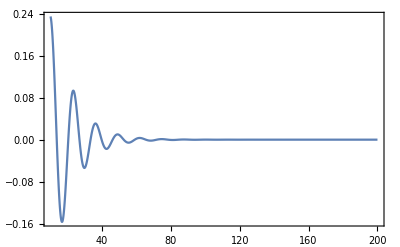

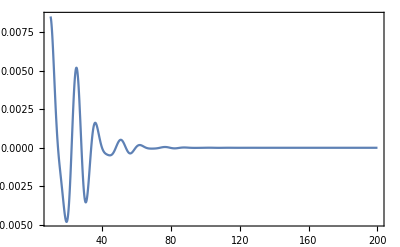

```mathematica
Plot[{Re[rdmod22]},{t,10,200},PlotRange->All,Frame->True,PlotLegends->"22"]
Plot[{Re[rdmod32]},{t,10,200},PlotRange->All,Frame->True,PlotLegends->"32"]
```